```mathematica
<<xlr8r.m;
<<Cellzilla2D.m
```

xCellerator 0.90 (2-Nov-2012) loaded Fri 9 Nov 2012 18:20:33
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

Cellzilla2D (2.3.6a (9-Nov-2012)) loaded Fri 9 Nov 2012 18:20:33
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

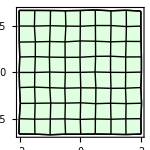

```mathematica
q=RandomizeTemplate[TemplateRectangular[{-2,2,.5},{-2, 2, .5}],.05];
Q=Tissue2DTissue[q];
ShowTissue[Q, Frame-> True]
```

```mathematica
network={};
diff={};
pumps={};
parameters={k->10,μ->.1,p->1.0};
```

```mathematica
SIM=grow[Q,0,25,
"Internal"-> True, 
"Show"-> False, 
"Reactions"-> network, 
"Pumps"-> pumps,
"Diffusion"-> diff, 
"WallReactions"->{},
"BoundaryConditions"-> {}, 
"EdgeVariable"-> ell,
"CellVariable"-> area,
"Growing"-> True,
"Restlength"-> resting,
"k"-> k,
"mu"-> μ, 
"P"-> p, 
"Parameters"-> parameters, 
"DivisionThreshold"-> 1000, 
"DivisionSigma"-> 0.15, 
"DivisionVariable"-> area
];
```

64 Cells.

0 internal reactions in each cell.

0 total intracellular reactions.

0 total intrawall reactions.

0 pump reactions.

0 diffusion reactions.

64 equations for cell area.

144 spring growth reactions.

162 spring reactions.

64 outer wall pressure reactions.

144 algebraic equations for spring growth.

370 total reactions.

snapshot$3234

Simulation Completed at t = 25. after 0 cell divisions; Normal Exit.

```mathematica
images=Show[GeometricSnapShot[Q, SIM, {x,y},{t, #}], PlotRange-> {{-3, 3}, {-3,3}}, PlotLabel-> "t="<>ToString[#]]&/@Range[0,25,5];
```

```mathematica
ListAnimate[images]
```